```mathematica
Quit
```

```mathematica
(* Here we use CMB shift params, DESI DR1 and Pantheon+ *)
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
obh2pl=0.02225;
ompl=0.3153;
s8pl=0.8111;
hpl=67.36/100;
obh2…BBN=0.02218;
```

```mathematica
files=FileNames["*.zip"];
```

```mathematica
params={"Ω_m","w_0","w_a","w_b","w_c","h"};
```

```mathematica
files
```

{bigchain_LCDM_v1.zip,bigchain_w0wa_v1.zip,bigchain_w0wawb_v1.zip,bigchain_w0wawbwc_v1_p1.zip,bigchain_w0wawbwc_v1_p2.zip,bigchain_w0wawbwc_v1_p3.zip,bigchain_wCDM_v1.zip}

```mathematica
chain…LCDM=Import["bigchain_LCDM_v1.zip",StringTake["bigchain_LCDM_v1.zip",{1,-5}]<>".m"];
chain…wCDM=Import["bigchain_wCDM_v1.zip",StringTake["bigchain_wCDM_v1.zip",{1,-5}]<>".m"];
chain…w0wa=Import["bigchain_w0wa_v1.zip",StringTake["bigchain_w0wa_v1.zip",{1,-5}]<>".m"];
chain…w0wawb=Import["bigchain_w0wawb_v1.zip",StringTake["bigchain_w0wawb_v1.zip",{1,-5}]<>".m"];
chain…w0wawbwc1=Import["bigchain_w0wawbwc_v1_p1.zip",StringTake["bigchain_w0wawbwc_v1_p1.zip",{1,-5}]<>".m"];
chain…w0wawbwc2=Import["bigchain_w0wawbwc_v1_p2.zip",StringTake["bigchain_w0wawbwc_v1_p2.zip",{1,-5}]<>".m"];
chain…w0wawbwc3=Import["bigchain_w0wawbwc_v1_p3.zip",StringTake["bigchain_w0wawbwc_v1_p3.zip",{1,-5}]<>".m"];
chain…w0wawbwc=Join[chain…w0wawbwc1,chain…w0wawbwc2,chain…w0wawbwc3];
```

```mathematica
chlen…LCDM=chain…LCDM//Length
chlen…wCDM=chain…wCDM//Length
chlen…w0wa=chain…w0wa//Length
chlen…w0wawb=chain…w0wawb//Length
chlen…w0wawbwc=chain…w0wawbwc//Length
```

369500

335913

292271

250374

732016

```mathematica
(* Best-fit from the MCMC *)
chi2min…LCDM=Min[chain…LCDM[[All,2]]]
bf…LCDM=chain…LCDM[[Position[chain…LCDM,chi2min…LCDM][[1,1]]]][[1]]
```

1439.41

{0.308746,0.677111}

```mathematica
chi2min…wCDM=Min[chain…wCDM[[All,2]]]
bf…wCDM=chain…wCDM[[Position[chain…wCDM,chi2min…wCDM][[1,1]]]][[1]]
```

1439.39

{0.309394,-0.996742,0.676303}

```mathematica
chi2min…w0wa=Min[chain…w0wa[[All,2]]]
bf…w0wa=chain…w0wa[[Position[chain…w0wa,chi2min…w0wa][[1,1]]]][[1]]
```

1430.24

{0.308297,-0.82092,-0.806888,0.680427}

```mathematica
chi2min…w0wawb=Min[chain…w0wawb[[All,2]]]
bf…w0wawb=chain…w0wawb[[Position[chain…w0wawb,chi2min…w0wawb][[1,1]]]][[1]]
```

1428.98

{0.307012,-0.952969,0.705318,-2.89421,0.68293}

```mathematica
chi2min…w0wawbwc=Min[chain…w0wawbwc[[All,2]]]
bf…w0wawbwc=chain…w0wawbwc[[Position[chain…w0wawbwc,chi2min…w0wawbwc][[1,1]]]][[1]]
```

1428.93

{0.306075,-1.06363,2.69582,-10.9335,8.69215,0.683696}

```mathematica
chi2s={chi2min…LCDM,chi2min…wCDM,chi2min…w0wa,chi2min…w0wawb,chi2min…w0wawbwc};
```

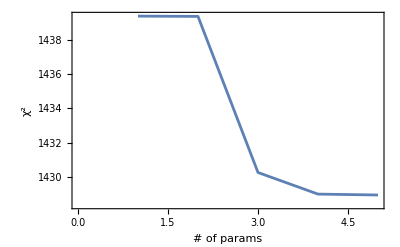

```mathematica
ListPlot[chi2s,Joined->True,Frame->True,FrameStyle->Black,FrameLabel->{"# of params","χ^2"}]
```

```mathematica
AIC[k_,chi2_]:=2k+chi2
```

```mathematica
ps={2,3,4,5,6};
mods={"ΛCDM","CPL-","CPL","CPL+","CPL++"};
```

```mathematica
Table[{mods[[i]],ps[[i]],chi2s[[i]],AIC[ps[[i]],chi2s[[i]]]},{i,1,5}]//TableForm
```

ΛCDM | 2 | 1439.41 | 1443.41
CPL- | 3 | 1439.39 | 1445.39
CPL | 4 | 1430.24 | 1438.24
CPL+ | 5 | 1428.98 | 1438.98
CPL++ | 6 | 1428.93 | 1440.93

```mathematica
Cijchain…LCDM=Covariance[chain…LCDM[[All,1,All]]]
PositiveDefiniteMatrixQ[Cijchain…LCDM]
SymmetricMatrixQ[Cijchain…LCDM]
Cijchain…LCDM//Diagonal//Sqrt
```

{{0.0000224021,-0.0000151028},{-0.0000151028,0.0000103163}}

True

True

{0.00473309,0.00321191}

```mathematica
Cijchain…wCDM=Covariance[chain…wCDM[[All,1,All]]]
PositiveDefiniteMatrixQ[Cijchain…wCDM]
SymmetricMatrixQ[Cijchain…wCDM]
Cijchain…wCDM//Diagonal//Sqrt
```

{{0.0000438489,0.000118025,-0.000043178},{0.000118025,0.000659237,-0.000155989},{-0.000043178,-0.000155989,0.0000472985}}

True

True

{0.00662185,0.0256756,0.00687739}

```mathematica
Cijchain…w0wa=Covariance[chain…w0wa[[All,1,All]]]
PositiveDefiniteMatrixQ[Cijchain…w0wa]
SymmetricMatrixQ[Cijchain…w0wa]
Cijchain…w0wa//Diagonal//Sqrt
```

{{0.0000458656,0.0000924808,0.00019894,-0.0000461393},{0.0000924808,0.00423336,-0.0173298,-0.0000690318},{0.00019894,-0.0173298,0.087853,-0.000526615},{-0.0000461393,-0.0000690318,-0.000526615,0.000052035}}

True

True

{0.00677242,0.0650642,0.2964,0.00721353}

```mathematica
Cijchain…w0wawb=Covariance[chain…w0wawb[[All,1,All]]]
PositiveDefiniteMatrixQ[Cijchain…w0wawb]
SymmetricMatrixQ[Cijchain…w0wawb]
Cijchain…w0wawb//Diagonal//Sqrt
```

{{0.0000482282,0.000250262,-0.00183966,0.00445117,-0.0000505515},{0.000250262,0.0215418,-0.219804,0.396295,-0.000357067},{-0.00183966,-0.219804,2.48318,-4.75494,0.00309047},{0.00445117,0.396295,-4.75494,9.60051,-0.0077557},{-0.0000505515,-0.000357067,0.00309047,-0.0077557,0.0000594231}}

True

True

{0.00694465,0.146771,1.57581,3.09847,0.00770864}

```mathematica
Cijchain…w0wawbwc=Covariance[chain…w0wawbwc[[All,1,All]]]
PositiveDefiniteMatrixQ[Cijchain…w0wawbwc]
SymmetricMatrixQ[Cijchain…w0wawbwc]
Cijchain…w0wawbwc//Diagonal//Sqrt
```

{{0.0000508258,0.000580536,-0.00799425,0.0305917,-0.029569,-0.00005285},{0.000580536,0.0511485,-0.786205,2.90246,-2.97566,-0.000667979},{-0.00799425,-0.786205,13.4354,-53.95,59.4546,0.00869763},{0.0305917,2.90246,-53.95,235.162,-279.093,-0.0299592},{-0.029569,-2.97566,59.4546,-279.093,354.313,0.0225914},{-0.00005285,-0.000667979,0.00869763,-0.0299592,0.0225914,0.0000616272}}

True

True

{0.00712922,0.22616,3.66543,15.335,18.8232,0.0078503}

```mathematica
(* χ^2 plot *)
Rasterize[ListPlot[chain…LCDM[[All,2]],Joined->True,PlotRange->{{0,1.02Length[chain…LCDM[[All,2]]]},chi2min…LCDM{0.995,1.05}},Frame->True,FrameLabel->{"N","χ^2"},FrameStyle->Black],RasterSize->2000]
```

```mathematica
Rasterize[ListPlot[chain…wCDM[[All,2]],Joined->True,PlotRange->{{0,1.02Length[chain…wCDM[[All,2]]]},chi2min…wCDM{0.995,1.05}},Frame->True,FrameLabel->{"N","χ^2"},FrameStyle->Black],RasterSize->2000]
```

```mathematica
Rasterize[ListPlot[chain…w0wa[[All,2]],Joined->True,PlotRange->{{0,1.02Length[chain…w0wa[[All,2]]]},chi2min…w0wa{0.995,1.05}},Frame->True,FrameLabel->{"N","χ^2"},FrameStyle->Black],RasterSize->2000]
```

```mathematica
Rasterize[ListPlot[chain…w0wawb[[All,2]],Joined->True,PlotRange->{{0,1.02Length[chain…w0wawb[[All,2]]]},chi2min…w0wawb{0.995,1.05}},Frame->True,FrameLabel->{"N","χ^2"},FrameStyle->Black],RasterSize->2000]
```

```mathematica
Rasterize[ListPlot[chain…w0wawbwc[[All,2]],Joined->True,PlotRange->{{0,1.02Length[chain…w0wawbwc[[All,2]]]},chi2min…w0wawbwc{0.995,1.05}},Frame->True,FrameLabel->{"N","χ^2"},FrameStyle->Black],RasterSize->2000]
```

```mathematica
orange=RGBColor["#FF9C27"];
green=RGBColor["#299D68"];
blue=RGBColor["#0273B2"];
magenta=RGBColor["#D38CC6"];
```

```mathematica
pp={2,3};
contour[par_,mcmc_,x_,y_,cols_]:=Module[{skd,pdf,cons},
skd=SmoothKernelDistribution[mcmc];
pdf=PDF[skd,mcmc];cons=Quantile[pdf,1-Erf[nn/(√2)]/.nn->{1,2}//N];ContourPlot[PDF[skd,{a,b}],{a,x[[1]],x[[2]]},{b, y[[1]], y[[2]]},Contours->cons,ContourShading->{Transparent,cols[[1]],cols[[2]]},BaseStyle->{FontFamily->"Times New Roman",FontSize->12},FrameStyle->Black,ClippingStyle->None,AspectRatio->1,ContourStyle->None,PlotRange->All]]
```

```mathematica
con…wCDM=ContourPlot[x,{x,-1.5,-0.3},{y,-10,10},Contours->(bf…wCDM[[2]]+Range[-2,2,1]Sqrt[Diagonal[Cijchain…wCDM]][[2]]),ContourShading->{Transparent,Lighter[magenta],magenta,magenta,Lighter[magenta],Transparent},BaseStyle->{FontFamily->"Times New Roman",FontSize->12},PlotRange->{{-1.7,-0.1},{-9,8}},FrameStyle->Black,ClippingStyle->None,AspectRatio->1,ContourStyle->{None,None,Darker[magenta],None,None}];
```

```mathematica
con…w0wa=contour[pp,chain…w0wa[[All,1,pp]],{-1,-0.5},{-2,0},{Lighter[blue],blue}];
```

```mathematica
con…w0wawb=contour[pp,chain…w0wawb[[All,1,pp]],{ -1.4,-0.5},{ -3,6},{Lighter[orange],orange}];
```

```mathematica
con…w0wawbwc=contour[pp,chain…w0wawbwc[[All,1,pp]],{-1.5,-0.3},{-10,8},{Lighter[green],green}];
```

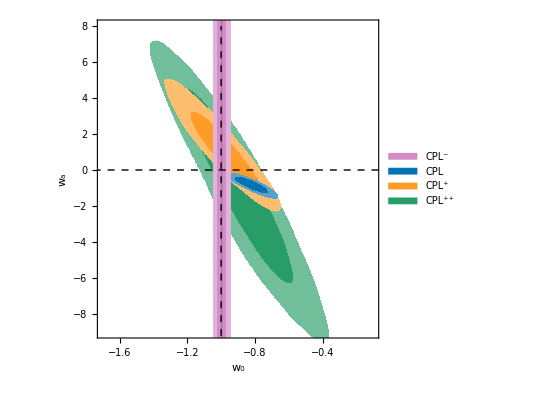

```mathematica
pl1=Show[Legended[Show[con…w0wawbwc,con…w0wawb,con…w0wa,con…wCDM,PlotRange->{{-1.7,-0.1},{-9,8}},Epilog->{{Dashed,Line[{{-1,-10},{-1,8}}]},{Dashed,Line[{{-2,0},{0,0}}]}}],Placed[SwatchLegend[{magenta,blue,orange,green},{Style["CPL^-",FontFamily->"Times New Roman"],Style["CPL",FontFamily->"Times New Roman"],Style["CPL^+",FontFamily->"Times New Roman"],Style["CPL^(++)",FontFamily->"Times New Roman"]}],Scaled[{0.86,0.77}]]],FrameLabel->params[[{2,3}]],ClippingStyle->Automatic,PlotRangeClipping->Automatic,ImageSize->400,BaseStyle->{FontFamily->"Times New Roman",FontSize->14}]
```

```mathematica
def={ompl,-1,0,0,0,hpl};
```

```mathematica
𝒟…wCDM…w0=SmoothKernelDistribution[chain…wCDM[[All,1,2]]];
max…wCDM…w0=Maximize[PDF[𝒟…wCDM…w0,x],x];

𝒟…w0wa…w0=SmoothKernelDistribution[chain…w0wa[[All,1,2]]];
max…w0wa…w0=Maximize[PDF[𝒟…w0wa…w0,x],x];

𝒟…w0wawb…w0=SmoothKernelDistribution[chain…w0wawb[[All,1,2]]];
max…w0wawb…w0=Maximize[PDF[𝒟…w0wawb…w0,x],x];

𝒟…w0wawbwc…w0=SmoothKernelDistribution[chain…w0wawbwc[[All,1,2]],.1];
max…w0wawbwc…w0=Maximize[PDF[𝒟…w0wawbwc…w0,x],x];
```

```mathematica
pl2=Plot[{PDF[𝒟…wCDM…w0,x]/max…wCDM…w0[[1]],PDF[𝒟…w0wa…w0,x]/max…w0wa…w0[[1]],PDF[𝒟…w0wawb…w0,x]/max…w0wawb…w0[[1]],PDF[𝒟…w0wawbwc…w0,x]/max…w0wawbwc…w0[[1]]},{x,-1.7,-0.1},Frame->True,PlotRange->{All,{-0.01,1.01}},AspectRatio->1,FrameLabel->{None,""},BaseStyle->{FontFamily->"Times New Roman",FontSize->13.5},Axes->False,FrameStyle->Black,PlotStyle->{magenta,blue,orange,green},Epilog->{Black,Dashed,Line[{{def[[2]],0},{def[[2]],10^3}}]},FrameTicksStyle->Transparent,ImageSize->600];
```

```mathematica
𝒟…w0wa…wa=SmoothKernelDistribution[chain…w0wa[[All,1,3]]];
max…w0wa…wa=Maximize[PDF[𝒟…w0wa…wa,x],x];

𝒟…w0wawb…wa=SmoothKernelDistribution[chain…w0wawb[[All,1,3]]];
max…w0wawb…wa=Maximize[PDF[𝒟…w0wawb…wa,x],x];

𝒟…w0wawbwc…wa=SmoothKernelDistribution[chain…w0wawbwc[[All,1,3]],1];
max…w0wawbwc…wa=Maximize[PDF[𝒟…w0wawbwc…wa,x],x];
```

```mathematica
pl3=Plot[{10^6 x,PDF[𝒟…w0wa…wa,x]/max…w0wa…wa[[1]],PDF[𝒟…w0wawb…wa,x]/max…w0wawb…wa[[1]],PDF[𝒟…w0wawbwc…wa,x]/max…w0wawbwc…wa[[1]]},{x,-9,8},Frame->True,PlotRange->{All,{-0.01,1.01}},AspectRatio->1,FrameLabel->{"w_a",None},BaseStyle->{FontFamily->"Times New Roman",FontSize->13.5},Axes->False,FrameStyle->Black,Epilog->{Black,Dashed,Line[{{def[[3]],0},{def[[3]],10^3}}]},PlotStyle->{magenta,blue,orange,green},FrameTicks->{{None,Automatic},{Automatic,None}},ImageSize->594];
```

```mathematica
plempty=Plot[0,{x,-1,1},Frame->True,Axes->False,PlotStyle->White,FrameStyle->{{White,White},{White,White}},FrameTicks->None,ImageSize->400];
```

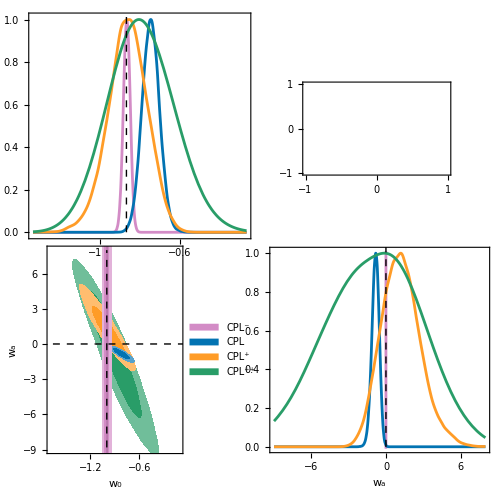

```mathematica
pl…cont=GraphicsGrid[{{pl2,plempty},{pl1,pl3}},ImageSize->500,Spacings->{-48.75,-64}]
```

```mathematica
Export["pl_cont.pdf",Rasterize[pl…cont,RasterSize->3000]]
```

pl_cont.pdf

```mathematica
ϵ={-1,0,1};
w[a_,w0_,wa_,wb_,wc_]:=w0+wa(1-a)+wb(1-a)^2+wc(1-a)^3
```

```mathematica
dw…w=D[w[a,w0,0,0,0],w0];
σw…w=Sqrt[dw…w Cijchain…wCDM[[2,2]] dw…w]//FullSimplify
```

0.0256756

```mathematica
dw…w0wa=D[w[a,w0,wa,0,0],{{w0,wa}}];
σw…w0wa=Sqrt[dw…w0wa.Cijchain…w0wa[[{2,3},{2,3}]].dw…w0wa]//FullSimplify
```

√(0.0574267+(-0.141046+0.087853 a) a)

```mathematica
dw…w0wawb=D[w[a,w0,wa,wb,0],{{w0,wa,wb}}];
σw…w0wawb=Sqrt[dw…w0wawb.Cijchain…w0wawb[[{2,3,4},{2,3,4}]].dw…w0wawb]//FullSimplify
```

√(2.94833+a (-15.9843+a (32.3492+a (-28.8922+9.60051 a))))

```mathematica
dw…w0wawbwc=D[w[a,w0,wa,wb,wc],{{w0,wa,wb,wc}}];
σw…w0wawbwc=Sqrt[dw…w0wawbwc.Cijchain…w0wawbwc[[{2,3,4,5},{2,3,4,5}]].dw…w0wawbwc]//FullSimplify
```

√(54.0672+a (-446.593+a (1534.96+a (-2806.84+a (2877.84+a (-1567.69+354.313 a))))))

```mathematica
w1=w[a,w0,0,0,0]+ϵ σw…w/.{w0->bf…wCDM[[2]]};
w2=w[a,w0,wa,0,0]+ϵ σw…w0wa/.{w0->bf…w0wa[[2]],wa->bf…w0wa[[3]]};
w3=w[a,w0,wa,wb,0]+ϵ σw…w0wawb/.{w0->bf…w0wawb[[2]],wa->bf…w0wawb[[3]],wb->bf…w0wawb[[4]]};
w4=w[a,w0,wa,wb,wc]+ϵ σw…w0wawbwc/.{w0->bf…w0wawbwc[[2]],wa->bf…w0wawbwc[[3]],wb->bf…w0wawbwc[[4]],wc->bf…w0wawbwc[[5]]};
ws=Flatten[{w4,w3,w2,w1}];
```

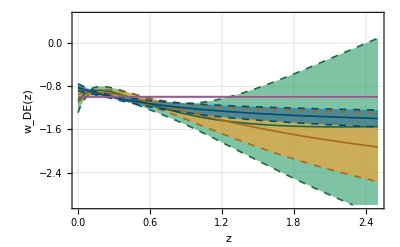

```mathematica
op=.6;
thick=0.003;
plws=Plot[ws/.a->1/(1+z)//Evaluate,{z,0,2.5},Frame->True,FrameStyle->Black,PlotStyle->{{Thickness[thick],Dashed,green//Darker},{Thickness[thick],green//Darker},{Thickness[thick],Dashed,green//Darker},{Thickness[thick],Dashed,orange//Darker},{Thickness[thick],orange//Darker},{Thickness[thick],Dashed,orange//Darker},{Thickness[thick],Dashed,blue//Darker},{Thickness[thick],blue//Darker},{Thickness[thick],Dashed,blue//Darker},None,{Thickness[thick],magenta//Darker},None},Filling->{1->{{3},{Opacity[op,green]}},4->{{6},{Opacity[op,orange]}},7->{{9},{Opacity[op,blue]}},10->{{12},{Opacity[op,magenta]}}},PlotRange->{{0,2.5},{-3,0.5}},FrameLabel->{"z","w_DE(z)"},Axes->False,BaseStyle->{FontFamily->"Times New Roman",FontSize->11},GridLines->Automatic]
```

```mathematica
Export["w_DE_z.pdf",plws]
```

w_DE_z.pdf

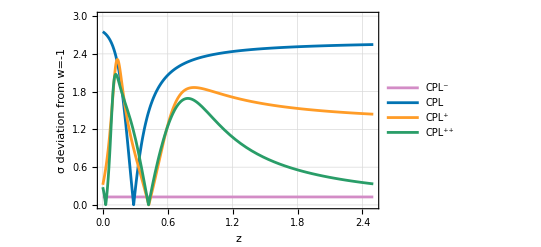

```mathematica
Plot[{(1+w1[[2]])/(σw…w),(1+w2[[2]])/(σw…w0wa),(1+w3[[2]])/(σw…w0wawb),(1+w4[[2]])/(σw…w0wawbwc)}/.a->1/(1+z)//Abs//Evaluate,{z,0,2.5},Frame->True,PlotRange->{{0,2.5},{0,3}},FrameStyle->Black,PlotStyle->{magenta,blue,orange,green},PlotLegends->{Style["CPL^-",FontFamily->"Times New Roman"],Style["CPL",FontFamily->"Times New Roman"],Style["CPL^+",FontFamily->"Times New Roman"],Style["CPL^(++)",FontFamily->"Times New Roman"]},FrameLabel->{"z","σ deviation from w=-1"},BaseStyle->{FontFamily->"Times New Roman",FontSize->12},GridLines->Automatic]
```

```mathematica
Solve[(w2[[2]]/.a->1/(1+z))==-1,z][[1]]//Quiet
```

{z→0.285247}

```mathematica
σ…av[zmin_,zmax_]:=1/(zmax-zmin)NIntegrate[{(1+w1[[2]])/(σw…w),(1+w2[[2]])/(σw…w0wa),(1+w3[[2]])/(σw…w0wawb),(1+w4[[2]])/(σw…w0wawbwc)}/.a->1/(1+z)//Abs,{z,zmin,zmax}]
```

```mathematica
{"CPL-","    CPL","    CPL+","   CPL++"}
σ…av[0,0.3]
σ…av[0,0.5]
σ…av[0,1]
σ…av[0,2]
σ…av[0,2.35]
```

{CPL-,    CPL,    CPL+,   CPL++}

{0.126886,1.79581,1.40151,1.32089}

{0.126886,1.56875,0.981162,0.977984}

{0.126886,1.88522,1.28413,1.21225}

{0.126886,2.18057,1.45259,1.01197}

{0.126886,2.23341,1.45617,0.923211}